## Procedures

### Procedures to get and set printing resolution for evaluation notebook

```mathematica
getPrintingResolutionForNotebook[] := 
Module[ {allOptions, printingOptions, newPrintingOptions},

allOptions = FullOptions[ EvaluationNotebook[] ];
printingOptions = PrintingOptions /. Cases[ allOptions, a_ /; First[ a ] === PrintingOptions ];

Cases[printingOptions, Verbatim[ Rule ][ "RasterizationResolution", _ ] ][[1]]
]
```

```mathematica
setPrintingResolutionForNotebook[ resolutionValueInDPI_ ] := 
Module[ {allOptions, printingOptions, newPrintingOptions},

allOptions = FullOptions[ EvaluationNotebook[] ];
printingOptions = PrintingOptions /. Cases[ allOptions, a_ /; First[ a ] === PrintingOptions ];

newPrintingOptions =  ReplaceAll[ printingOptions, Verbatim[ Rule ][ "RasterizationResolution", _ ]  :>   Rule[ "RasterizationResolution", resolutionValueInDPI  ] ];

SetOptions[ EvaluationNotebook[], PrintingOptions -> newPrintingOptions ]
]
```

```mathematica
setPrintingResolutionForNotebook[ 72 * 4 ]
```

### Procedure to set headers

```mathematica
setTestHeaders[ whatSubjectCode_, whatSemester_, whatYear_, whatTest_, isSolutionQ_, durationString_ ] := 
Module[ {nb, changingString, subjectCodeString},
nb = EvaluationNotebook[];

changingString = StringJoin[  "American University of Malta\n",
 whatSemester ,
" ",
If[ StringQ[ whatYear ] === True, whatYear, ToString[ whatYear ] ],
Which[ (isSolutionQ && Not[ StringQ[ whatTest ] ]) === True, " - Solution to Test ", 
(Not[ isSolutionQ ] && Not[ StringQ[ whatTest ] ]) === True, " - Test ", 
True, " " ], 
Which[ StringQ[ whatTest ] === True, whatTest, True, ToString[ whatTest ] ],
"  ",
If[durationString === "", "", "("],
Which[ StringQ[ durationString ], durationString,
durationString === Automatic, "1 hr 0 min",
True, "1 hr 0 min" ],
If[durationString === "", "", ")"]
];
subjectCodeString = If[ StringQ[ whatSubjectCode ] === True, whatSubjectCode, ToString[ whatSubjectCode ] ];


SetOptions[ nb,PageHeaders->{{Cell[TextData[{StyleBox[ subjectCodeString <> "\nN Fares",FontFamily->"Times",FontSize->12]}],"Text"],Cell[TextData[{StyleBox[changingString,FontFamily->"Times",FontSize->12]}],"Text"],Cell[TextData[{StyleBox["Page ",FontFamily->"Times",FontSize->12],CounterBox["Page"]}],"Text"]},{Cell[TextData[{StyleBox[subjectCodeString <> "\nN Fares",FontFamily->"Times",FontSize->12]}],"Text"],Cell[TextData[{StyleBox[changingString,FontFamily->"Times",FontSize->12]}],"Text"],Cell[TextData[{StyleBox["Page ",FontFamily->"Times",FontSize->12],CounterBox["Page"]}],"Text"]}},
PrintingOptions->{"FacingPages"->True,"FirstPageFace"->Right,"FirstPageFooter"->True,"FirstPageHeader"->True}]
]
```

```mathematica
$Fall = "Fall";
$Spring = "Spring";
```

### Load package

```mathematica
<<NFPackages`structuralMechanicsBook` // Quiet;
```

## Preparation

### Problem 1

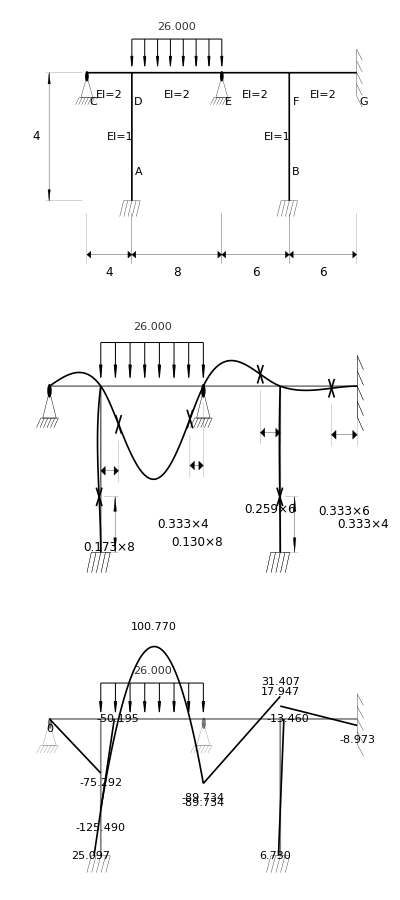

```mathematica
makeBuildingVerticalSpecsAndSolutionGrid[ {4}, {4, 8, 6, 6},300,
buildingBeamUniformLoadList -> { {1, 2} -> 26},
buildingBeamPointForceList -> { },
buildingNodeMomentApplied -> {},
buildingNodeMomentLabel-> "20",
buildingBeamsEIMagnitudeList -> {_ -> 2},
buildingBeamsEILabelList -> {},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingColumnOmitList -> { {1, 1} -> True, {1, 2} -> False, {1, 3} -> True, {1, 4} -> False, {1, 5} -> True},
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {},
buildingSideSupportRightList -> { _ -> "fixed"},
buildingSupportList -> {1 -> "hinge", 2 -> "fixed"},
buildingFactorMomentDiagrams -> 0.0025,
buildingDimensionLabelHeightList-> {},
buildingDimensionLabelSpanList -> { },
buildingSolveColumnBeamDisplacementFunctions -> False ]
```

#### Problem statement

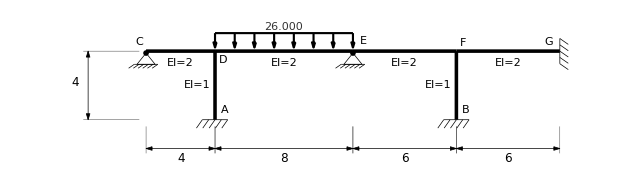

a) Sketch the deflected shape marking all locations of inflection points.
b) Sketch the moment diagram for all the frame members.

#### Solution

a) Sketch the deflected shape marking all locations of inflection points.

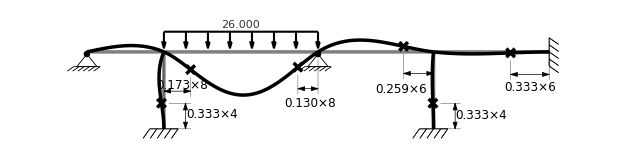

b) Sketch the moment diagram for all the frame members.

-Graphics-

### Problem 2

```mathematica
Manipulate[Column[{
{α, α/(1-α)},
makeBuildingVerticalSpecsAndSolutionGrid[ {0.1}, { α * 10, (1-α) * 10, (1-α) * 10, α * 10},300,
buildingBeamUniformLoadList -> { {1, 1} -> 100, {1, 2} -> 100, {1, 3} -> 100, {1, 4} -> 100},
buildingBeamPointForceList -> { },
buildingNodeMomentApplied -> {},
buildingNodeMomentLabel-> "20",
buildingUniformLoadLabel -> "w",
buildingBeamsEIMagnitudeList -> {_ -> 1},
buildingBeamsEILabelList -> {{1, 1} -> "EI", {1, 2} -> "EI"},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingColumnOmitList -> { {1, 1} -> True, {1, 2} -> True, {1, 3} -> True, {1, 4} -> True, {1, 5} -> True},
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {},
buildingSideSupportRightList -> { _ -> None},
buildingSupportList -> {1 -> "hinge", 2 -> "hinge", 3 -> "hinge", 4 -> "hinge", 5-> "hinge"},
buildingFactorMomentDiagrams -> 0.0025,
buildingDimensionLabelHeightList-> {_ -> None},
buildingDimensionLabelSpanList -> { 1->"αL",2-> "(1-α)L",3-> "(1-α)L",4-> "αL"},
buildingSolveColumnBeamDisplacementFunctions -> False ]}],
{{α, 0.5}, 0.05, 0.95, 0.01}]
```

```mathematica
Manipulate[Column[{
{α, α/(1-α)},
makeBuildingVerticalSpecsAndSolutionGrid[ {0.1}, { α * 10, (1-α) * 10},300,
buildingBeamUniformLoadList -> { {1, 1} -> 100, {1, 2} -> 100},
buildingBeamPointForceList -> { },
buildingNodeMomentApplied -> {},
buildingNodeMomentLabel-> "20",
buildingUniformLoadLabel -> "w",
buildingBeamsEIMagnitudeList -> {_ -> 1},
buildingBeamsEILabelList -> {{1, 1} -> "EI", {1, 2} -> "EI", {1, 3} -> "EI", {1, 4} -> "EI", {1, 5} -> "EI"},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingColumnOmitList -> { {1, 1} -> True, {1, 2} -> True, {1, 3} -> True, {1, 4} -> True, {1, 5} -> True},
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {},
buildingSideSupportRightList -> { _ -> None},
buildingSupportList -> {1 -> "hinge", 2 -> "hinge", 3 -> "hinge", 4 -> "hinge", 5 -> "hinge"},
buildingFactorMomentDiagrams -> 0.0025,
buildingDimensionLabelHeightList-> {_ -> None},
buildingDimensionLabelSpanList -> { 1->"αL",2-> "(1-α)L",3-> "(1-α)L",4-> "αL"},
buildingSolveColumnBeamDisplacementFunctions -> False ]}],
{{α, 0.5}, 0.01, 0.5, 0.01}]
```

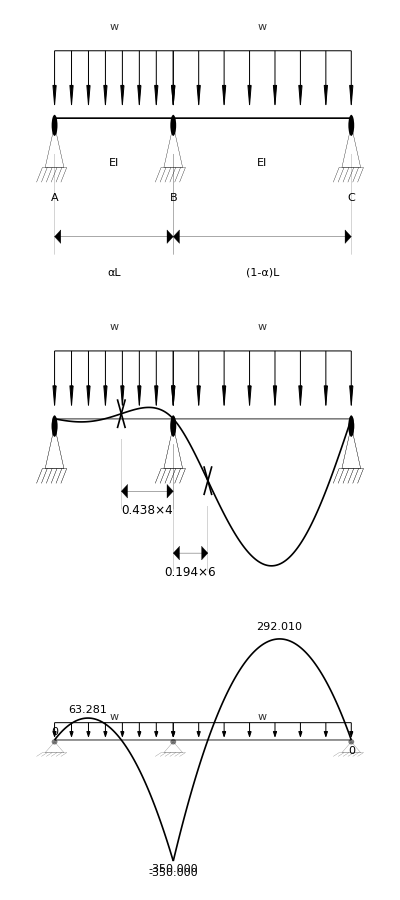

```mathematica
makeBuildingVerticalSpecsAndSolutionGrid[ {0.1}, {4, 6},300,
buildingBeamUniformLoadList -> { {1, 1} -> 100, {1, 2} -> 100},
buildingBeamPointForceList -> { },
buildingNodeMomentApplied -> {},
buildingNodeMomentLabel-> "20",
buildingUniformLoadLabel -> "w",
buildingBeamsEIMagnitudeList -> {_ -> 1},
buildingBeamsEILabelList -> {{1, 1} -> "EI", {1, 2} -> "EI"},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingColumnOmitList -> { {1, 1} -> True, {1, 2} -> True, {1, 3} -> True, {1, 4} -> False, {1, 5} -> True},
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {},
buildingSideSupportRightList -> { _ -> None},
buildingSupportList -> {1 -> "hinge", 2 -> "hinge"},
buildingFactorMomentDiagrams -> 0.0025,
buildingDimensionLabelHeightList-> {_ -> None},
buildingDimensionLabelSpanList -> { 1->"αL",2-> "(1-α)L"},
buildingSolveColumnBeamDisplacementFunctions -> False ]
```

#### Problem Statement

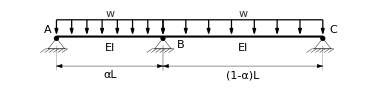

The total length of the two-span beam is “L” (αL + (1-α)L = L).
How do the following bending moments vary with α for 0 ≤ α ≤ 1/2:
a) Maximum positive moment in AB
b) Negative moment at B

#### Solution

a) Maximum positive moment in AB

The maximum positive moment in AB increases with α in the range 0 ≤ α ≤ 1/2

b) Negative moment at B

The maximum negative moment at B decreases with α in the range 0 ≤ α ≤ 1/2

## Assignment

### Set title

```mathematica
setTestHeaders[ "CIE 418", $Fall, 2022, "Assignment 2", False, "" ]
```

### Problem 1

#### Problem statement

-Graphics-

a) Sketch the deflected shape marking all locations of inflection points.
b) Sketch the moment diagram for all the frame members.

### Problem 2

-Graphics-

The total length of the two-span beam is “L” (αL + (1-α)L = L).
How do the following bending moments vary with α for 0 ≤ α ≤ 1/2:
a) Maximum positive moment in AB
b) Negative moment at B

## Assignment Solution

### Set title

```mathematica
setTestHeaders[ "CIE 418", $Fall, 2022, "Solution to Assignment 2", False, "" ]
```

### Problem 1

-Graphics-

a) Sketch the deflected shape marking all locations of inflection points.
b) Sketch the moment diagram for all the frame members.

#### Solution

a) Sketch the deflected shape marking all locations of inflection points.

-Graphics-

b) Sketch the moment diagram for all the frame members.

-Graphics-

### Problem 2

-Graphics-

The total length of the two-span beam is “L” (αL + (1-α)L = L).
How do the following bending moments vary with α for 0 ≤ α ≤ 1/2:
a) Maximum positive moment in AB
b) Negative moment at B

#### Solution

a) Maximum positive moment in AB

The maximum positive moment in AB increases with α in the range 0 ≤ α ≤ 1/2

b) Negative moment at B

The maximum negative moment at B decreases with α in the range 0 ≤ α ≤ 1/2